```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
SeedRandom[1];
<<"Sampler3`";
(*pos def, neg def, indef, ring*)
SIGMA={{0.6999999999999998,0.9999999999999999},{0.9999999999999999,0.6999999999999998}};
SIGMA={{1,.7},{.7,1}};
U[x_,y_]=1/2 Simplify[{x,y}.LinearSolve[SIGMA,{x,y}]];
σ=1;
U[x_,y_]=1/(2 σ^2)(√(x^2+y^2)-10.)^2;
```

```mathematica
dU[x_,y_]=GradientG[U[x,y],{x,y}];
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
dddU[x_,y_]=D3[U[x,y],{x,y}];
```

```mathematica
traj1[dU_,dKdp_,dKdq_,r_,q0_,p0_,dt_,steps_]:=Module[{q=q0,p=p0},
Prepend[Table[
q=q+dt Apply[dKdp,{p,q,r}];
p=p- dt( Apply[dU,q]+ Apply[dKdq,{p,q,r}]);
Append[q,Apply[U,q]],steps],Append[q0,Apply[U,q0]]]];
```

```mathematica
SeedRandom[2];
dt=.01;
steps=2000;
```

```mathematica
q0=RandomVariate[NormalDistribution[0,1],2]
q0={11,1};
q00=Append[q0,Apply[U,q0]];
p0=RandomVariate[NormalDistribution[0,1],2];
QS1=traj1[dU,dKdp,dKdq,1,q0,p0,dt,steps];
p0=RandomVariate[NormalDistribution[0,1],2];
QS2=traj1[dU,dKdp,dKdq,2,q0,p0,dt,steps];
p0=RandomVariate[NormalDistribution[0,1],2];
q0=RandomVariate[NormalDistribution[0,1],2]
q0={-3,8};
q01=Append[q0,Apply[U,q0]];
QS3=traj1[dU,dKdp,dKdq,1,q0,p0,dt,steps];
p0=RandomVariate[NormalDistribution[0,1],2];
QS4=traj1[dU,dKdp,dKdq,2,q0,p0,dt,steps];
```

{0.623366,0.512066}

{0.0993941,-0.744493}

```mathematica
QS1//Dimensions
```

{2001,3}

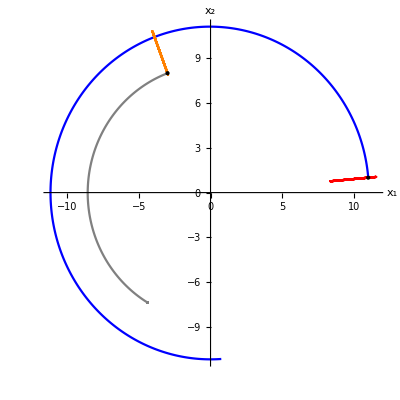

```mathematica
GraphicsRow[{Show[ListPointPlot3D[{QS1,QS2,QS3,QS4},AxesLabel->{"x_1","x_2","U"},PlotStyle->{Directive[Dashing,Red],Directive[Dashing,Blue],Directive[Dashing,Orange],Directive[Dashing,Gray]}],Graphics3D[Point[q00]],Graphics3D[Point[q01]],Graphics3D[Join[{Red},Map[Line[#]&,Partition[QS1,2,1]]]],Graphics3D[Join[{Blue},Map[Line[#]&,Partition[QS2,2,1]]]],Graphics3D[Join[{Orange},Map[Line[#]&,Partition[QS3,2,1]]]],Graphics3D[Join[{Black},Map[Line[#]&,Partition[QS4,2,1]]]]],Show[ListPlot[{QS1[[;;,1;;2]],QS2[[;;,1;;2]],QS3[[;;,1;;2]],QS4[[;;,1;;2]]},Joined->True,AxesLabel->{"x_1","x_2","U"},PlotStyle->{Directive[Red],Directive[Blue],Directive[Orange],Directive[Gray]},AspectRatio->1],Graphics[Point[q00[[1;;2]]]],Graphics[Point[q01[[1;;2]]]]]}]
```